InitializationObjects

```mathematica
(*Returns a Normal Vector for a line between two points*)
normalVector[{{x2_,y2_},{x1_,y1_}}]:=Normalize[{(-y2+y1),x2-x1} ]
```

```mathematica
(*Returns a Vector for a line between two points*)
vector[{{x2_,y2_},{x1_,y1_}}]:={x2-x1,y2-y1}
```

```mathematica
convexMinkowskiSum[robot_,obstacle_]:=Module[{robotLines,obstacleLines,robotVectors,obstacleVectors,mergedVectors,prev={0,0}},
(* This function assumes that both polyObstacle and polyRobot are an ordered list of the vertices of two convex polygons. Authors: Arifa, Shreyas, and Aaron, Date: Feb 07, 2019*)
(*Convert points of polygons as a list of two points representing a line*)
robotLines= Partition[Append[robot,First[robot]],2,1];
obstacleLines=Partition[Append[obstacle,First[obstacle]],2,1];
(*Calculate the Normal & Vector of lines(direction inwards for robot & outwards for Obstacles)*)
robotVectors= {(- normalVector[#]),-vector[#]}&/@robotLines; 
obstacleVectors={normalVector[#],vector[#]}&/@obstacleLines;
(*get the Angle of Normal vectors and merge and sort the vectors w.r.t angles*)
mergedVectors = Sort[{ArcTan[#⟦1⟧⟦1⟧,#⟦1⟧⟦2⟧],#⟦2⟧}&/@Join [robotVectors,obstacleVectors],#1⟦1⟧<#2⟦1⟧&];
(*subtract the vector from the prev point to get the current point *)
(*change name*)RotateLeft[(Chop[prev=prev-#⟦2⟧])&/@mergedVectors,-1]
]
```

```mathematica
convexMinkowskiSumRev1[robot_,obstacle_]:=Module[{lineList,robotVectors,obstacleVectors,sortedVectors,prev={0,0}},
(* This function assumes that both polyObstacle and polyRobot are an ordered list of the vertices of two convex polygons. Authors: Arifa, Shreyas, and Aaron, Date: Feb 12, 2019*)
(*Returns Nested list of two points representing a Line*)
lineList[list_]:=Partition[Append[list,First[list]],2,1];
(*Get the Normal & the Vector of lines*) (*Normals & vectors are Inwards for robot &Outwards for Obstacles*)
robotVectors= {(- normalVector[#]),-vector[#],#}&/@lineList@robot; 
obstacleVectors={normalVector[#],vector[#],#}&/@lineList@obstacle;
(*get the Angle of Normal vectors and merge and sort the vectors w.r.t angles*)
sortedVectors = SortBy[{ArcTan[#⟦1⟧⟦1⟧,#⟦1⟧⟦2⟧],#⟦2⟧,#⟦3⟧}&/@Join [robotVectors,obstacleVectors],First];
(*Get the Minkowski by adding the vectors in the sorted order*)
RotateLeft[(Chop[prev=prev-#⟦2⟧])&/@sortedVectors,-1]
]
```

```mathematica
findConvexHullCoordsConvexPolysAS[polyObstacle_,polyRobot_]:=Module[{pts},
(* this function assumes that both polyObstacle and polyRobot are an ordered list of the vertices of two convex polygons. Authors: Arifa, Shreyas, and Aaron, Date: Jan 2, 2019*)
(*First, place the robot at each vertix of the obstacle, and record the vertices coordinates, then flatten this list*)
pts =Flatten[ Table[polyObstacle⟦1,i⟧- polyRobot⟦1,j⟧,{i,1,Length[polyObstacle⟦1⟧]},{j,1,Length[polyRobot⟦1⟧]}],1];
(*second, grab an ordered list of convex hull of these points*)#["Coordinates"][[#["BoundaryVertices"]⟦1⟧]]&@ConvexHullMesh[pts]
]
```

Demo code

```mathematica
Manipulate[
Module[{robot,obstacle,robotLines,obstacleLines,robotNormal,obstacleNormal,robotArrows,obstacleArrows,robotAssignedNormal,obstacleAssignedNormal,mergedNormals,orderOfNormals,sortedArrows,sortedSides,rc,oc,sortedNormals,robotlabel,obstcalelabel,robotSubscript,obstacleSubscript,prev,minkowskiPoints},

(*Generate the robot & obstacle points*)
robot =pts⟦1;;m⟧;
obstacle =pts⟦6;;n+5⟧;
rc=Mean@robot;
oc=Mean@obstacle;
(*robot =(rc+r-#)&/@robot;*)

(*Make a list having a set of two points a element *)
robotLines= Partition[Append[robot,First[robot]],2,1];
obstacleLines=Partition[Append[obstacle,First[obstacle]],2,1];

(*Get the Robot and Obstacle Normals*)
robotNormal = {(- normalVector[#]),-vector[#],#}&/@robotLines; (* Robot inwards*)
obstacleNormal={normalVector[#],vector[#],#}&/@obstacleLines;

(*Make Arrows on inside the polygons*)
robotArrows=Arrow[{Median[#⟦3⟧],0.5#⟦1⟧+Median[#⟦3⟧]}]&/@robotNormal; 
obstacleArrows = Arrow[{Median[#⟦3⟧],0.5#⟦1⟧+Median[#⟦3⟧]}]&/@obstacleNormal;	

(*Create Sub script*)
robotSubscript=Cases[Range[1,Length[robotNormal]],t:_:>Subscript[α, t]];
obstacleSubscript=Cases[Range[1,Length[obstacleNormal]],t:_:>Subscript[β, t]];

(*Assign the Edges of robot with α and obstacle as /[Beta]*)
robotAssignedNormal =AssociationThread[robotSubscript-> robotNormal];
obstacleAssignedNormal =AssociationThread[obstacleSubscript-> obstacleNormal];

(*Merge the Normals & add the angles in the value list*)
mergedNormals ={ArcTan[#⟦1⟧⟦1⟧,#⟦1⟧⟦2⟧],#⟦1⟧,#⟦2⟧,#⟦3⟧}&/@Join [robotAssignedNormal,obstacleAssignedNormal];

(*Sort the Normals based on angles*)
orderOfNormals = Sort[mergedNormals,#1⟦1⟧<#2⟦1⟧&];

(*Get the Minkowski Sum*)
(*prev={0,0};
minkowskiPoints=(Chop[prev=prev-#⟦3⟧])&/@Values@orderOfNormals;*)

minkowskiPoints=(*({4,-4}+#)&/@*)convexMinkowskiSumRev2[robot,obstacle];

(*Make Arrows*) 
sortedArrows=Arrow[{{-3,0},{-3,0}+#⟦2⟧}]&/@Values[orderOfNormals];

(*Draw Text*)
robotlabel = Table[Text[Keys[robotAssignedNormal]⟦i⟧,(Median@robotAssignedNormal⟦i⟧⟦3⟧-0.2robotAssignedNormal⟦i⟧⟦1⟧)],{i,1,Length[robotAssignedNormal],1}];
obstcalelabel = Table[Text[Keys[obstacleAssignedNormal]⟦i⟧,(Median@obstacleAssignedNormal⟦i⟧⟦3⟧-0.2obstacleAssignedNormal⟦i⟧⟦1⟧)],{i,1,Length[obstacleAssignedNormal],1}];
sortedSides = Table[Text[Keys[orderOfNormals]⟦i⟧,{-3,0}+1.2orderOfNormals⟦i⟧⟦2⟧],{i,1,Length[orderOfNormals],1}]; 

 
Graphics[
{EdgeForm[Thin]
(*,{White,Polygon@(({2.1213,2.1213}+#)&/@(3*CirclePoints[4])),
Polygon@(({-2.1213,2.1213}+#)&/@(3*CirclePoints[4])),Polygon@(({-2.1213,-2.1213}+#)&/@(3*CirclePoints[4])),Polygon@(({2.1213,-2.1213}+#)&/@(3*CirclePoints[4]))}*)
,If[configOrWork=="work"
,{{LightGreen,Opacity[0.5], Polygon@(({4,-4}+#)&/@minkowskiPoints)}
,{LightRed, Polygon@obstacle}
,{Opacity[0.5],LightBlue, Polygon@robot}
,{obstacleArrows,robotArrows}
,{Blue,robotlabel}
,{Red,obstcalelabel}
,{sortedArrows,sortedSides}
,{Red,Point@robot,Point@obstacle}
,{White,Disk[{-3,0},{0.5,0.5}]}
},

{White,Polygon@(5CirclePoints[4]),{LightGreen,Opacity[0.5], Polygon@((#-oc)&/@minkowskiPoints)}
,{LightRed, Polygon@((#-oc)&/@obstacle)}
,{Opacity[0.5],LightBlue, Polygon@((rc+r-#)&/@robot)}
}]
}]
]
,{{configOrWork,"work","Space"},{"work","config"}}
,{{pts,{{0.5,3.24},{0.41,2.25},{1.565,2.08},{1.465,3.54}
,{0.735,3.59},{-2.4,2.19},{-2.048,3.30},{-3,4},{-3.95,3.30},{-3.5,2.13}}},{-5,-5},{5,5},ControlType->None,Appearance->None}
,{{m,4,"Robot Edges"},3,5,1,SetterBar}
,{{n,5,"Obstacle Edges"},3,5,1,SetterBar}
,{{r,{0,3}},{-5,-5},{5,5},ControlType->None}
]
```

#### Force polyomonio to stay convex (hide vertiex if non convex) make prettiere *convert to Demo add description outline robot in blue, object in red, color code the lines on the Minkowski sum to match the original edges, maybe allow showing/hiding the normals β -> blue α->red

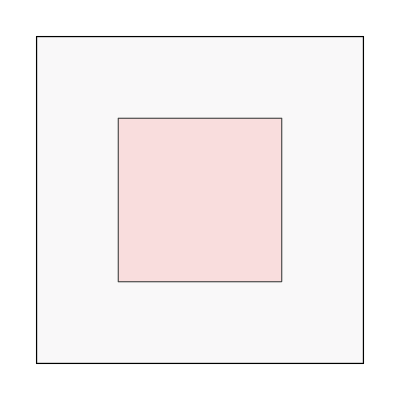

```mathematica
robot =N[CirclePoints[4]];
obstacle = N[CirclePoints[4]];
hull=findConvexHullCoordsConvexPolysAS[Polygon@obstacle,Polygon@robot];
norm=convexMinkowskiSumRev2[robot,obstacle];
Graphics[{EdgeForm[Thin],{ LightRed,Polygon@obstacle},{Opacity[0.2],LightPurple,Polygon@hull},{Opacity[0.1],LightGreen,Polygon@norm}}]
```

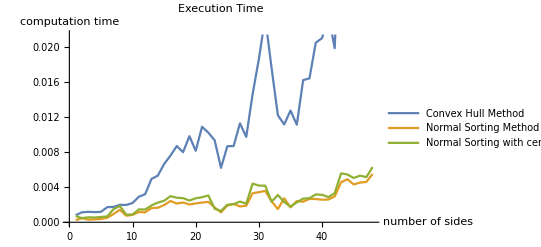

```mathematica
result=Table[robot =N[CirclePoints[i]];
obstacle =N[CirclePoints[i]];{AbsoluteTiming[findConvexHullCoordsConvexPolysAS[Polygon@obstacle,Polygon@robot]]⟦1⟧,
AbsoluteTiming[convexMinkowskiSumRev1[robot,obstacle]]⟦1⟧,
AbsoluteTiming[convexMinkowskiSumRev2[robot,obstacle]]⟦1⟧}
,{i,3,50,1}];
ListLinePlot[Transpose@result,PlotLegends->{"Convex Hull Method","Normal Sorting Method","Normal Sorting with centroid shifted"},AxesLabel->{"number of sides","computation time"},PlotLabel->"Execution Time"]
```

```mathematica
reflex[{x1_,y1_},{x2_,y2_},{x3_,y3_}]:=Chop[Det[({{1, x1, y1}, {1, x2, y2}, {1, x3, y3}})]>0]
```

```mathematica
nonConvexVertexIndex[polyg_]:=Module[{p=Join[polyg,polyg]⟦1;;-2⟧,l=Length@polyg-1,list={}},
(If[reflex[p⟦#⟧,p⟦#+1⟧,p⟦#+2⟧],AppendTo[list,p⟦#+1⟧]])&/@Range[Length@p-2];list
]
```

{{1.91,2.25},{3.065,2.08},{2.965,3.54},{2.235,3.59},{2.,3.24},{1.91,2.25},{3.065,2.08}}

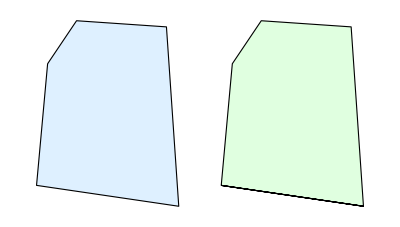

```mathematica
robot =N[CirclePoints[3]];
r1={{0.5,3.24},{0.41,2.25},{1.565,2.08}, 
  {1.465,3.54}, {0.735,3.59}};
r2=({1.5,0}+#)&/@nonConvexVertexIndex[r1]
Graphics[{EdgeForm[Thin],{LightBlue,Polygon@r1},{Opacity[1],LightGreen,Polygon@r2}}]
```

```mathematica
convexMinkowskiSumRev2[robot_,obstacle_]:=Module[{lineList,robotVectors,obstacleVectors,sortedVectors,prev,rc=Mean@robot,pos},
(* This function assumes that both polyObstacle and polyRobot are an ordered list of the vertices of two convex polygons. Authors: Arifa, Shreyas, and Aaron, Date: Feb 12, 2019*)
(*Returns Nested list of two points representing a Line*)
lineList[list_]:=Partition[Append[list,First[list]],2,1];
(*Get the Normal & the Vector of lines*) (*Normals & vectors are Inwards for robot &Outwards for Obstacles*)
robotVectors= {(- normalVector[#]),-vector[#],α,#}&/@lineList@robot; 
obstacleVectors={normalVector[#],vector[#],β,#}&/@lineList@obstacle;
(*get the Angle of Normal vectors and merge and sort the vectors w.r.t angles*)
sortedVectors = SortBy[{ArcTan[#⟦1⟧⟦1⟧,#⟦1⟧⟦2⟧],#⟦2⟧,#⟦3⟧,#⟦4⟧}&/@Join [robotVectors,obstacleVectors],First];
(*Get the start point which is prev*)
pos=SequencePosition[sortedVectors⟦;;,3⟧,{α,β}]⟦1,1⟧;
prev=rc+sortedVectors⟦pos+1⟧⟦4⟧⟦1⟧ -sortedVectors⟦pos⟧⟦4⟧⟦1⟧;
(*Get the Minkowski by adding the vectors in the sorted order*)
(Chop[prev=prev-#⟦2⟧])&/@RotateLeft[sortedVectors,pos-1]
]
```

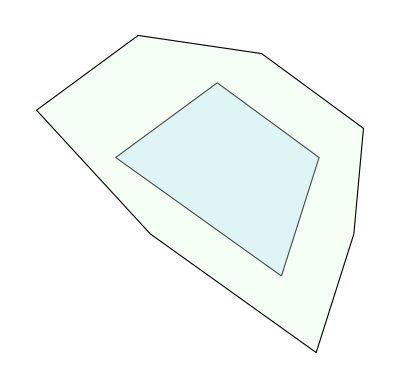

```mathematica
robot ={{0.5,3.24},{0.41,2.25},{1.565,2.08}};
obstacle = {{-2.4,2.19},{-2.048,3.30},{-3,4},{-3.95,3.30}};
oc=Mean@obstacle;
(*rc=Mean@robot;
oc=Mean@obstacle;
sortedVectors=convexMinkowskiSumRev2[robot,obstacle];
seqpos=SequencePosition[sortedVectors⟦;;,3⟧,{"α","β"}]⟦1,1⟧;
prev=rc+sortedVectors⟦seqpos+1⟧⟦4⟧⟦1⟧ -sortedVectors⟦seqpos⟧⟦4⟧⟦1⟧;
sortedVectors = RotateLeft[sortedVectors,seqpos-1];
mink=(Chop[prev=prev-#⟦2⟧])&/@sortedVectors;*)
mink=convexMinkowskiSumRev2[robot,obstacle];
Graphics[{EdgeForm[Thin],{LightBlue,Polygon@obstacle,Opacity[0.3],LightGreen,Polygon@mink}}]
```

```mathematica
TabView[{x->(a),y->b,z->c}]
```

123

```mathematica
OpenerView[{"Plot",Plot[Sin[x],{x,0,2 Pi}]}]
```

```mathematica
MenuView[{40!,Plot[Sin[x],{x,0,2 Pi}],Factor[x^14-1]}]
```

```mathematica
PopupView[Table[i!,{i,20}]]
```

```mathematica
FlipView[{40!,Plot[Sin[x],{x,0,2 Pi}],Factor[x^14-1]}]
```

```mathematica
OpenerView[{"Title","Contents"}]
```

```mathematica
Toggler[6,Table[{i,i!},{i,10}]]
```

```mathematica
Manipulate[TabView[{{"patt","Pattern"->type},{"motif","Motif"->Grid[{{Column[{Button["Line",type=Line,ImageSize->100],Button["Bezier",type=BezierCurve,ImageSize->100],Button["Point",type=Point,ImageSize->100]}],Graphics[type[{{0,0},{1,0},{0,1}}]]}}]}},Dynamic[choice]],{{type,Line},None},{{choice,"patt"},None}]
```

```mathematica
N@CirclePoints[4]
```

{{0.707107,-0.707107},{0.707107,0.707107},{-0.707107,0.707107},{-0.707107,-0.707107}}

```mathematica
3*0.70710
```

2.1213